```mathematica
Needs["ErrorBarPlots`"];

(* temperature, min hours, max hours *)
values = {{-30,8, 9},{-25,12,13},{-18,20, 22}};
v = {{#[[1]], Mean[Rest[#]] //N}, ErrorBar[(#[[3]]-#[[2]])/2]} & /@ values
```

```mathematica
{{{-30,8.5},ErrorBar[1/2]},{{-25,12.5},ErrorBar[1/2]},{{-18,21.},ErrorBar[1]}}
```

{{{-30,8.5},ErrorBar[1/2]},{{-25,12.5},ErrorBar[1/2]},{{-18,21.},ErrorBar[1]}}

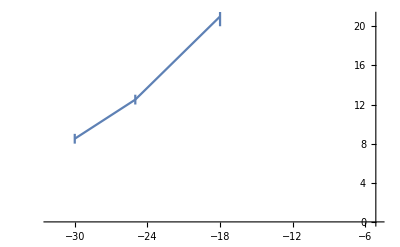

{2,3}

```mathematica
ErrorListPlot[v, Joined->True, PlotRange -> {{-32,-5}, Automatic}]
```